ClearAll::wrsym: Symbol D is Protected.

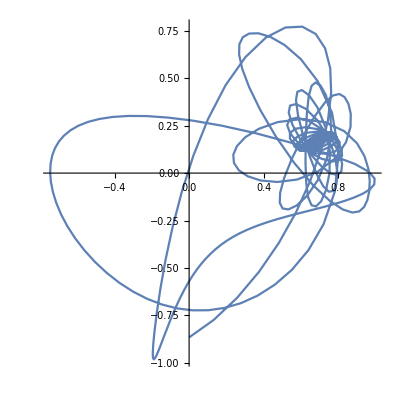

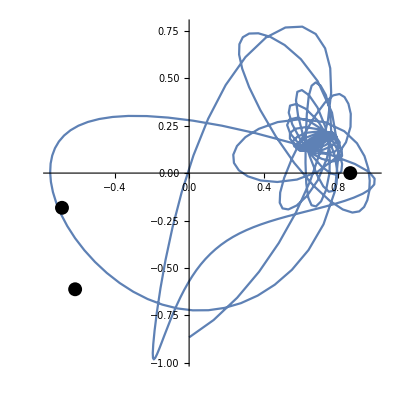

```mathematica
ClearAll[sol,s,D];
g=9.81;
l=1;
a1=Pi;
a2=Pi/4;
a3=Pi/12;
s1=2*Pi/3;
s2=2*Pi/3;
s3=Pi/4;
f1=1/Cos[s1];
f2=1/Cos[s2];
f3=1/Cos[s3];
q1=50;
q2=-8;
q3=-7;
q4=-10;
ϵ=1E-2;
m=1;
Cd=1;

system={θ''[t]==((ϕ'[t]^2* Cos[θ[t]]*Sin[θ[t]]-(g/l)*Sin[θ[t]]-((q1*q2)/(m*l*l*ϵ*8*Pi*(l^2+f1^2-2*l*f1*(Sin[θ[t]]*Sin[s1]*Cos[ϕ[t]-a1]+Cos[θ[t]]*Cos[s1]))^(3/2)))*(2*l*f1*(Cos[θ[t]]*Sin[s1]*Cos[ϕ[t]-a1]-Sin[θ[t]]*Cos[s1])))
-((q1*q3)/(m*l*l*ϵ*8*Pi*(l^2+f2^2-2*l*f2*(Sin[θ[t]]*Sin[s2]*Cos[ϕ[t]-a2]+Cos[θ[t]]*Cos[s2]))^(3/2))*(2*l*f2*(Cos[θ[t]]*Sin[s2]*Cos[ϕ[t]-a2]-Sin[θ[t]]*Cos[s2])))
-((q1*q4)/(m*l*l*ϵ*8*Pi*(l^2+f3^2-2*l*f3*(Sin[θ[t]]*Sin[s3]*Cos[ϕ[t]-a3]+Cos[θ[t]]*Cos[s3]))^(3/2))*(2*l*f3*(Cos[θ[t]]*Sin[s3]*Cos[ϕ[t]-a3]-Sin[θ[t]]*Cos[s3]))))-Cd*θ'[t],ϕ''[t]==(((((q1*q2)/(m*l*l*ϵ*8*Pi*(l^2+f1^2-2*l*f1*(Sin[θ[t]]*Sin[s1]*Cos[ϕ[t]-a1]+Cos[θ[t]]*Cos[s1]))^(3/2)))*(2*f1*l*Sin[θ[t]]*Sin[s1]*Sin[ϕ[t]-a1])-(2 ϕ'[t] θ'[t] *Sin[θ[t]]*Cos[θ[t]]))

+((q1*q3)/(m*l*l*ϵ*8*Pi*(l^2+f2^2-2*l*f2*(Sin[θ[t]]*Sin[s2]*Cos[ϕ[t]-a2]+Cos[θ[t]]*Cos[s2]))^(3/2)))*(2*f2*l*Sin[θ[t]]*Sin[s2]*Sin[ϕ[t]-a2])+((q1*q4)/(m*l*l*ϵ*8*Pi*(l^2+f3^2-2*l*f3*(Sin[θ[t]]*Sin[s3]*Cos[ϕ[t]-a3]+Cos[θ[t]]*Cos[s3]))^(3/2)))*(2*f3*l*Sin[θ[t]]*Sin[s3]*Sin[ϕ[t]-a3]))/(Sin[θ[t]]*Sin[θ[t]]))-Cd*ϕ'[t]

,θ[0]==2*Pi/3,θ'[0]==10,ϕ[0]==3*Pi/2,ϕ'[0]==10};


sol=Flatten@ NDSolve[system, {θ,ϕ},{t,0,50},PrecisionGoal->8,AccuracyGoal->8,Method->"StiffnessSwitching"];

x[t_]:=(Sin[θ[t]] Cos[ϕ[t]])
y[t_]:=(Sin[θ[t]] Sin[ϕ[t]])
z[t_]:=-Cos[θ[t]]

plot = ParametricPlot[{x[t],y[t]}/.sol,{t,0,50},PlotRange->All, Evaluated->True]

Show[plot,Graphics[{PointSize[0.025],Point[{-1*Sin[s1]*Cos[a1],-1*Sin[s1]*Sin[a1]}],Point[{-1*Sin[s2]*Cos[a2],-1*Sin[s2]*Sin[a2]}],Point[{-1*Sin[s3]*Cos[a3],-1*Sin[s3]*Sin[a3]}]}]]
Animate[ParametricPlot3D[{x[t],y[t],z[t]}/.sol,{t,0,h},AxesLabel->z,PlotRange->All,Evaluated->True],{h,0,30}]
```